# GGX Specular BRDF

```mathematica
Clear["Global`*"]
ggx[μ_,α_]:=α^2/(π(μ^2(α^2-1)+1)^2)
smith[θ_,α_]:=1/(Cos[θ]+√(α^2+(1-α^2)*Cos[θ]^2))
(* change[] gives cos(Subscript[θ, h]) when provided with Subscript[ω, i] and Subscript[ω, o] *)
change[θo_,θi_,ϕi_]:=(Cos[θo]+Cos[θi])/(√(2*(1+Cos[θo]*Cos[θi]+Sin[θo]*Sin[θi]*Cos[ϕi])))
```

Let’s test our formulas:

```mathematica
Plot3D[ggx[Cos[x],y],{x,0,π/2},{y,0.001,1}]
Plot3D[smith[x,y],{x,0,π/2},{y,0.001,1},PlotRange->{0,2},AxesLabel->{"θ","α","Smith"}]
change[0,π/2,0]
```

-Graphics3D-

-Graphics3D-

1/(√2)

```mathematica
Manipulate[Plot3D[change[θo,θ,ϕ],{θ,0,π/2},{ϕ,-π,π},PlotRange->{0,1},AxesLabel->{"θ_i","ϕ_i","θ_h"}],{{θo,0},0,π/2}]
```

```mathematica
Clear[θ,α]
(* Makes no sense since smith is in macro space and ggx in half-vector space *)
(*Integrate[smith[θ,α]*ggx[θ,α]*Cos[θ]*Sin[θ],{θ,0,π/2},Assumptions->{α>0,α<=1}]*)
```

```mathematica
Clear[θi,ϕ,α]
(* This takes ages to complete and returns the stupid terms expansion below *)
(*Integrate[smith[θi,α]*ggx[change[θi,θo,ϕ],α]*Cos[θi]*Sin[θi],{θi,0,π/2},Assumptions->{α>0,α<=1,θo≥0,θo<π/2,ϕ>=-π,ϕ<=π}]*)
```

Here we verify that, ignoring Fresnel at the moment, whatever the roughness the total specular reflectance over the entire hemisphere is always 1:

```mathematica
Manipulate[2π*Integrate[ggx[Cos[θ],α]*Cos[θ]*Sin[θ],{θ,0,π/2}],{{α,0.5},0.001,1}]
```

But if we make the masking/shadowing term intervene, then the integral is not 1 anymore as soon as the roughness != 0:
Actually, makes no sense since smith is in macro space while NDF is in half-vector space!

```mathematica
(*Manipulate[2π*Integrate[smith[θ,α]*ggx[θ,α]*Cos[θ]*Sin[θ],{θ,0,π/2}],{α,0.001,1}]*)
```

### Numerical Integration

Let’s try Mathematica’s numerical integration instead and see if we can go faster:

```mathematica
(* Don't evaluate that! Takes FOREVER! *)
(*Ei[θo_,ϕ_,α_]:=Integrate[smith[θi,α]*ggx[change[θo,θi,ϕ],α] * Cos[θi]* Sin[θi],{θi,0,π/2}]*)
Ei[0,0,0.5]
```

Ei[0,0,0.5]

```mathematica
Ei[θo_,ϕ_,α_]:=NIntegrate[smith[θi,α]*ggx[change[θo,θi,ϕ],α] * Cos[θi]* Sin[θi],{θi,0,π/2}]
θo=0;
ϕ=0;
α=0.5;
Ei[0,0,0.5]
```

0.218949

Indeed it IS faster! :D

Technically, the expression we need to evaluate is this:

```mathematica
Eo[θo_,α_]:=smith[θo,α]*Integrate[Integrate[smith[θi,α]*ggx[change[θo,θi,ϕi],α] * Cos[θi]* Sin[θi],{θi,0,π/2}],{ϕi,-π,π}]
```

With numerical integration we get instead

```mathematica
ϕi = -π;
θo=0.1;
α=0.5;
NIntegrate[smith[θi,α]*ggx[change[θo,θi,ϕi],α] * Cos[θi]* Sin[θi],{θi,0,π/2}]
```

0.247075

```mathematica
θo=0.2;
α=0.005;
smith[θo,α]*NIntegrate[smith[θi,α]*ggx[change[θo,θi,ϕi],α] * Cos[θi]* Sin[θi],{θi,0,π/2},{ϕi,-π,π}]
(*smith[θo,α]*NIntegrate[Ei[θo,ϕi,α],{ϕi,-π,π}]*)
```

0.999974

Finally, we can build the final expression for irradiance:

```mathematica
Eo[θo_,α_]:=smith[θo,α]*NIntegrate[smith[θi,α]*ggx[change[θo,θi,ϕi],α] * Cos[θi]* Sin[θi],{θi,0,π/2},{ϕi,-π,π}]
Eo[0.1,0.5]
```

0.687578

```mathematica
α=0.9;
2*π*NIntegrate[smith[θo,α]*smith[θi,α]*ggx[change[θo,θi,ϕi],α] *Cos[θi]*Sin[θi]*Cos[θo]*Sin[θo],{θi,0,π/2},{ϕi,-π,π},{θo,0,π/2},WorkingPrecision->MachinePrecision]
```

1.34166

## Building the Table of Irradiance Values

So let’s build a table of these values!

```mathematica
countX = 128;
countY= 128;
buildTable=Function[{i},
x=N[Mod[i,countX]/(countX-1)];
y=N[Quotient[i,countX]/(countY-1)];
θo=ArcCos[x];
α=Max[0.01,y];
{x,y,N[Eo[θo,α]]}
]
buildTable[128*5+17]
```

Function[{i},x=N[Mod[i,countX]/(countX-1)];y=N[Quotient[i,countX]/(countY-1)];θo=ArcCos[x];α=Max[0.01,y];{x,y,N[Eo[θo,α]]}]

{0.133858,0.0393701,0.952105}

```mathematica
Manipulate[buildTable[i],{i,0,countX*countY-1,1}]
```

```mathematica
resultEo= Table[buildTable[i],{i,0,countX*countY-1}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

$Aborted

```mathematica
ListPlot3D[resultEo]
Image[Table[Table[1-resultEo[[1+countX*y+x]][[3]],{x,0,countX-1}],{y,0,countY-1}]]
```

-Graphics3D-

-Graphics-

```mathematica
SetDirectory["D:\\Workspaces\\GodComplex\\Tests\\TestMSBRDF\\Tables"]; 
Export["MSBRDF_E128x128.csv",resultEo,"CSV"]
```

MSBRDF_E128x128.csv

```mathematica
testResultEo = Import["MSBRDF_E128x128.csv","CSV"];
ListPlot3D[testResultEo,AxesLabel->{"cos(θ)", "α","E_i"}]
```

-Graphics3D-

Let’s reorder the table and create an interpolation function from it:

```mathematica
t=Table[testResultEo[[1+countX*(y-1)+(x-1)]][[3]],{x,1,countY},{y,1,countY}];
fEo=ListInterpolation[t,{{0,1},{0,1}}]
Plot3D[fEo[x,y],{x,0,1},{y,0,1},AxesLabel->{"cos(θ)", "α","E_i"}]
```

InterpolatingFunction[{{0., 1.}, {0., 1.}}, <>]

-Graphics3D-

## Computing Average Irradiance

Now let’s integrate the full white furnace irradiance using our table:

	E_avg(α)=∫E_o(θ_o,α) cos(θ_o) ⅆ θ_o

```mathematica
resultEavg=Table[{N[i/(countY-1)],2*π*NIntegrate[fEo[μ,i/(countY-1)]μ,{μ,0,1}]},{i,0,countY-1}]
```

{{0.,3.13998},{0.00787402,3.13998},{0.015748,3.13794},{0.023622,3.13408},{0.0314961,3.12913},{0.0393701,3.12321},{0.0472441,3.1164},{0.0551181,3.10877},{0.0629921,3.10038},{0.0708661,3.09129},{0.0787402,3.08155},{0.0866142,3.07118},{0.0944882,3.06023},{0.102362,3.04874},{0.110236,3.03673},{0.11811,3.02424},{0.125984,3.01128},{0.133858,2.99789},{0.141732,2.98409},{0.149606,2.96991},{0.15748,2.95535},{0.165354,2.94045},{0.173228,2.92522},{0.181102,2.90967},{0.188976,2.89384},{0.19685,2.87773},{0.204724,2.86136},{0.212598,2.84474},{0.220472,2.82789},{0.228346,2.81083},{0.23622,2.79356},{0.244094,2.7761},{0.251969,2.75847},{0.259843,2.74066},{0.267717,2.72271},{0.275591,2.70461},{0.283465,2.68638},{0.291339,2.66802},{0.299213,2.64956},{0.307087,2.63099},{0.314961,2.61233},{0.322835,2.59359},{0.330709,2.57477},{0.338583,2.55589},{0.346457,2.53695},{0.354331,2.51796},{0.362205,2.49892},{0.370079,2.47985},{0.377953,2.46076},{0.385827,2.44164},{0.393701,2.42251},{0.401575,2.40337},{0.409449,2.38423},{0.417323,2.3651},{0.425197,2.34597},{0.433071,2.32687},{0.440945,2.30778},{0.448819,2.28872},{0.456693,2.26969},{0.464567,2.2507},{0.472441,2.23175},{0.480315,2.21285},{0.488189,2.194},{0.496063,2.1752},{0.503937,2.15646},{0.511811,2.13778},{0.519685,2.11917},{0.527559,2.10065},{0.535433,2.08216},{0.543307,2.06377},{0.551181,2.04545},{0.559055,2.02722},{0.566929,2.00908},{0.574803,1.99102},{0.582677,1.97305},{0.590551,1.95517},{0.598425,1.93739},{0.606299,1.91971},{0.614173,1.90213},{0.622047,1.88464},{0.629921,1.86726},{0.637795,1.84999},{0.645669,1.83282},{0.653543,1.81576},{0.661417,1.79882},{0.669291,1.78198},{0.677165,1.76525},{0.685039,1.74864},{0.692913,1.73215},{0.700787,1.71577},{0.708661,1.6995},{0.716535,1.68336},{0.724409,1.66733},{0.732283,1.65142},{0.740157,1.63564},{0.748031,1.61997},{0.755906,1.60443},{0.76378,1.589},{0.771654,1.5737},{0.779528,1.55852},{0.787402,1.54347},{0.795276,1.52853},{0.80315,1.51373},{0.811024,1.49904},{0.818898,1.48448},{0.826772,1.47004},{0.834646,1.45572},{0.84252,1.44153},{0.850394,1.42746},{0.858268,1.41352},{0.866142,1.3997},{0.874016,1.386},{0.88189,1.37242},{0.889764,1.35897},{0.897638,1.34564},{0.905512,1.33242},{0.913386,1.31934},{0.92126,1.30637},{0.929134,1.29352},{0.937008,1.28079},{0.944882,1.26818},{0.952756,1.2557},{0.96063,1.24333},{0.968504,1.23107},{0.976378,1.21894},{0.984252,1.20692},{0.992126,1.19502},{1.,1.18323}}

```mathematica
Export["MSBRDF_Eavg128.csv",resultEavg,"CSV"]
```

MSBRDF_Eavg128.csv

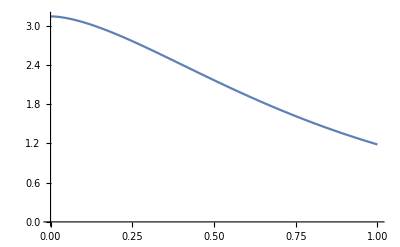

```mathematica
ListLinePlot[resultEavg]
```

InterpolatingFunction[{{0., 1.}}, <>]

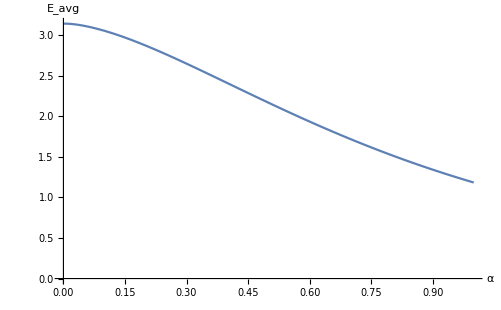

```mathematica
t=Table[resultEavg[[i]][[2]],{i,1,countY}];
fEavg=ListInterpolation[t,{0,1}]
Plot[fEavg[x],{x,0,1},PlotRange->{0,π}, AxesLabel->{"α","E_avg"}]
```

Export as binary float arays for C#:

```mathematica
t=Table[testResultEo[[i]][[3]],{i,1,countX*countY}];
Export["MSBRDF_E128x128.float",t,"Real32"]
t=Table[resultEavg[[i]][[2]],{i,1,countY}];
Export["MSBRDF_Eavg128.float",t,"Real32"]
```

MSBRDF_E128x128.float

MSBRDF_Eavg128.float

### Fitting Eavg

{a→0.,b→-0.446898,c→-5.72019,d→6.61848,e→-2.41727}

π-0.446898 x-5.72019 x^2+6.61848 x^3-2.41727 x^4

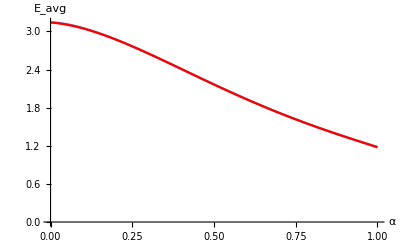

```mathematica
Clear[a,b,c,d,x]
fittingMethod="LevenbergMarquardt";
fittingMethod="PrincipalAxis";
fittingMethod="Automatic";

modelEavg=π+0*a+(0+1*b)*x+c*x^2+d*x^3+e*x^4;
fitEavg=FindFit[resultEavg,modelEavg,{a,b,c,d,e},x,Method->fittingMethod]
modelEavg/.fitEavg
funcEavg=Function[x,Evaluate[modelEavg/.fitEavg]];
Show[
Plot[fEavg[x],{x,0,1},PlotRange->{0,π},AxesLabel->{"α","E_avg"}],
Plot[funcEavg[x],{x,0,1},PlotStyle->Red]
]
```

## Let’s check the BRDFs sum to π!

```mathematica
BRDFggx[θo_,θi_,ϕ_,α_]:= smith[θo,α]*smith[θi,α]*ggx[change[θo,θi,ϕi],α]
BRDFms[θo_,θi_,ϕ_,α_]:=((1-fEo[Cos[θo],α])*(1-fEo[Cos[θi],α]))/(π-fEavg[α])
```

```mathematica
whiteFurnace0[α_]:=2*π*NIntegrate[BRDFggx[θo,θi,ϕ,α]*Cos[θi]*Sin[θi]*Cos[θo]*Sin[θo],{θi,0,π/2},{ϕi,-π,π},{θo,0,π/2},WorkingPrecision->MachinePrecision]
whiteFurnace1[α_]:=2*π*NIntegrate[BRDFms[θo,θi,ϕ,α]*Cos[θi]*Sin[θi]*Cos[θo]*Sin[θo],{θi,0,π/2},{ϕi,-π,π},{θo,0,π/2},WorkingPrecision->MachinePrecision]
```

```mathematica
whiteFurnace0[0.3]
whiteFurnace1[0.3]
```

2.64771

0.493886

```mathematica
whiteFurnaceResult0=Table[{α,whiteFurnace0[Max[0.01,α]]},{α,0,1,0.05}]
whiteFurnaceResult1=Table[{α,whiteFurnace1[Max[0.01,α]]},{α,0,1,0.05}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.499733 and 0.0000510937 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.495579 and 1.18889×10^-6 for the integral and error estimates.

{{0.,3.13991},{0.05,3.11382},{0.1,3.05224},{0.15,2.96919},{0.2,2.87121},{0.25,2.76289},{0.3,2.64771},{0.35,2.52841},{0.4,2.4072},{0.45,2.28586},{0.5,2.16582},{0.55,2.0482},{0.6,1.93385},{0.65,1.82343},{0.7,1.7174},{0.75,1.61607},{0.8,1.51963},{0.85,1.42816},{0.9,1.34166},{0.95,1.26005},{1.,1.18323}}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000314469 and 6.88027×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

{{0.,0.00197587},{0.05,0.0277751},{0.1,0.0893483},{0.15,0.172407},{0.2,0.270382},{0.25,0.378701},{0.3,0.493886},{0.35,0.613187},{0.4,0.734392},{0.45,0.855729},{0.5,0.975771},{0.55,1.0934},{0.6,1.20774},{0.65,1.31816},{0.7,1.42419},{0.75,1.52552},{0.8,1.62196},{0.85,1.71343},{0.9,1.79993},{0.95,1.88154},{1.,1.95836}}

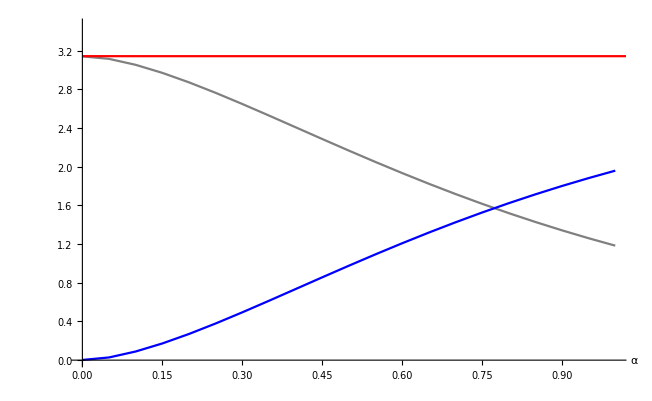

```mathematica
Show[
ListLinePlot[whiteFurnaceResult0,PlotRange->{0,1.1*π},PlotStyle->Gray,AxesLabel->{"α",""}],
ListLinePlot[whiteFurnaceResult1,PlotStyle->Blue],
ListLinePlot[whiteFurnaceResult0+whiteFurnaceResult1,PlotRange->Full,PlotStyle->Red]
]
```

# Oren-Nayar Diffuse BRDF

### Plotting Oren-Nayar Coefficients

Just to make sure the standard deviation σ is in radians! (they keep giving it in degrees, I started to be a bit skeptical for a moment)...

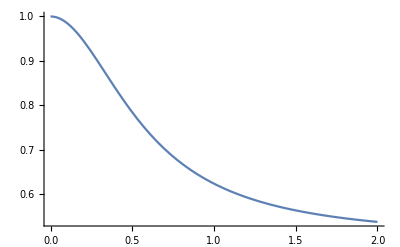

```mathematica
Plot[1-0.5 σ^2/(σ^2+0.33),{σ,0,2}]
```

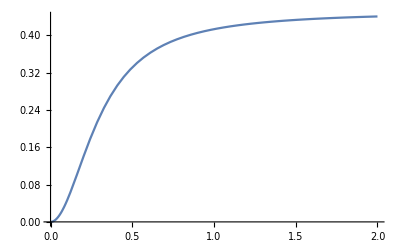

```mathematica
Plot[0.45 σ^2/(σ^2+0.09),{σ,0,2}]
```

```mathematica
oren=Function[ {θo,ϕo,θi,ϕi,α},
σ=π/2 α;
A = 1-0.5*σ^2/(σ^2+0.33);
B = 0.45*σ^2/(σ^2+0.09);
a=Max[θo,θi];
b=Min[θo,θi];
1/π(A+B*Max[0,Cos[ϕo-ϕi]]*Sin[a]*Tan[b])
];
oren[0,0,0.1,0.2,0.2]
```

0.281669

```mathematica
Manipulate[Plot3D[oren[θo,0,x,0,α],{x,0,π/2},{α,0,1},PlotRange->{0,1},AxesLabel->{"cos(θ)","α","Oren"}],{{θo,π/2},0,π/2}]
```

Let’s try integrating the Lambertian case:

```mathematica
α=0.0;
2*π*NIntegrate[oren[θo,0,θi,ϕi,α]*Cos[θi]*Sin[θi]*Cos[θo]*Sin[θo],{θi,0,π/2},{ϕi,-π,π},{θo,0,π/2}]
```

3.14159

```mathematica
orenEo[θo_,α_]:=NIntegrate[oren[θo,0,θi,ϕi,α] * Cos[θi]* Sin[θi],{θi,0,π/2},{ϕi,-π,π}]
orenEo[0.5,0.4]
```

0.769888

```mathematica
SetDirectory["D:\\Workspaces\\GodComplex\\Tests\\TestMSBRDF\\Tables"]; 
countX = 32;
countY= 32;
tableFileName="MSBRDF_OrenNayar_E"  <>ToString[countX] <>"x" <> ToString[countY] <>".csv"
tableFileNameAvg="MSBRDF_OrenNayar_Eavg"  <>ToString[countY] <>".csv"

buildTable=Function[{i},
x=N[Mod[i,countX]/(countX-1)];
y=N[Quotient[i,countX]/(countY-1)];
θo=ArcCos[x];
α=y;
{x,y,Min[1,orenEo[θo,α]]}
]
buildTable[countX*5+7]
```

MSBRDF_OrenNayar_E32x32.csv

MSBRDF_OrenNayar_Eavg32.csv

Function[{i},x=N[Mod[i,countX]/(countX-1)];y=N[Quotient[i,countX]/(countY-1)];θo=ArcCos[x];α=y;{x,y,Min[1,orenEo[θo,α]]}]

{0.225806,0.16129,Min[1,orenEo[1.34303,0.16129]]}

```mathematica
resultOrenEo= Table[buildTable[i],{i,0,countX*countY-1}];
Export[tableFileName,resultOrenEo,"CSV"]
```

MSBRDF_OrenNayar_E32x32.csv

```mathematica
Export[tableFileName,resultOrenEo,"CSV"]
```

```mathematica
ListPlot3D[resultOrenEo,PlotRange->{0,1},AxesLabel->{"cos(θ_o)","α"}]
Image[Table[Table[1-resultOrenEo[[1+countX*y+x]][[3]],{x,0,countX-1}],{y,0,countY-1}]]
```

-Graphics3D-

-Graphics-

Re-Importing and testing...

```mathematica
resultOrenEo = Import[tableFileName,"CSV"];
ListPlot3D[resultOrenEo,AxesLabel->{"cos(θ)", "α","E_i"}]
```

-Graphics3D-

Let’s reorder the table and create an interpolation function from it:

```mathematica
t=Table[resultOrenEo[[1+countX*(y-1)+(x-1)]][[3]],{x,1,countY},{y,1,countY}];
fOrenEo=ListInterpolation[t,{{0,1},{0,1}}]
Plot3D[fOrenEo[x,y],{x,0,1},{y,0,1},AxesLabel->{"cos(θ)", "α","E_i"}]
```

InterpolatingFunction[{{0., 1.}, {0., 1.}}, <>]

-Graphics3D-

## Computing Average Irradiance

Now let’s integrate the full white furnace irradiance using our table:

	E_avg(α)=∫E_o(θ_o,α) cos(θ_o) ⅆ θ_o

```mathematica
resultOrenEavg=Table[{N[i/(countY-1)],2*π*NIntegrate[fOrenEo[μ,i/(countY-1)]μ,{μ,0,1}]},{i,0,countY-1}]
Export[tableFileNameAvg,resultOrenEavg,"CSV"]
```

{{0.,3.14159},{0.0322581,3.13724},{0.0645161,3.12342},{0.0967742,3.09846},{0.129032,3.06099},{0.16129,3.01112},{0.193548,2.95093},{0.225806,2.88414},{0.258065,2.81461},{0.290323,2.74519},{0.322581,2.67792},{0.354839,2.61412},{0.387097,2.55455},{0.419355,2.49955},{0.451613,2.44916},{0.483871,2.40324},{0.516129,2.36154},{0.548387,2.32375},{0.580645,2.28953},{0.612903,2.25857},{0.645161,2.23053},{0.677419,2.20513},{0.709677,2.18209},{0.741935,2.16116},{0.774194,2.14212},{0.806452,2.12477},{0.83871,2.10894},{0.870968,2.09446},{0.903226,2.0812},{0.935484,2.06903},{0.967742,2.05785},{1.,2.04755}}

MSBRDF_OrenNayar_Eavg32.csv

```mathematica
resultOrenEavg=Import[tableFileNameAvg,"CSV"]
```

{{0.,3.14159},{0.0322581,3.13724},{0.0645161,3.12342},{0.0967742,3.09846},{0.129032,3.06099},{0.16129,3.01112},{0.193548,2.95093},{0.225806,2.88414},{0.258065,2.81461},{0.290323,2.74519},{0.322581,2.67792},{0.354839,2.61412},{0.387097,2.55455},{0.419355,2.49955},{0.451613,2.44916},{0.483871,2.40324},{0.516129,2.36154},{0.548387,2.32375},{0.580645,2.28953},{0.612903,2.25857},{0.645161,2.23053},{0.677419,2.20513},{0.709677,2.18209},{0.741935,2.16116},{0.774194,2.14212},{0.806452,2.12477},{0.83871,2.10894},{0.870968,2.09446},{0.903226,2.0812},{0.935484,2.06903},{0.967742,2.05785},{1.,2.04755}}

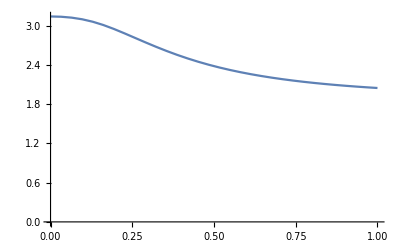

```mathematica
ListLinePlot[resultOrenEavg,PlotRange->{0,π}]
```

InterpolatingFunction[{{0., 1.}}, <>]

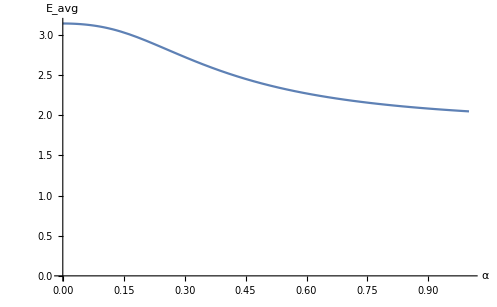

```mathematica
t=Table[resultOrenEavg[[i]][[2]],{i,1,countY}];
fOrenEavg=ListInterpolation[t,{0,1}]
Plot[fOrenEavg[x],{x,0,1},PlotRange->{0,π}, AxesLabel->{"α","E_avg"}]
```

{a→0.,b→0.,c→-7.49231,d→11.4409,e→-5.05903}

π-7.49231 x^2+11.4409 x^3-5.05903 x^4

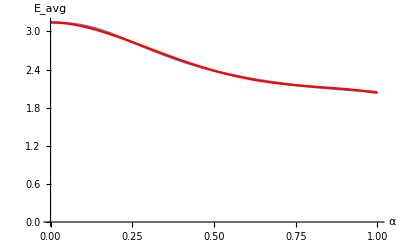

```mathematica
Clear[a,b,c,d,x]
fittingMethod="LevenbergMarquardt";
fittingMethod="PrincipalAxis";
fittingMethod="Automatic";

modelOrenEavg=π+0*a+(0+0*b)*x+c*x^2+d*x^3+e*x^4;
fitOrenEavg=FindFit[resultOrenEavg,modelOrenEavg,{a,b,c,d,e},x,Method->fittingMethod]
modelOrenEavg/.fitOrenEavg
funcOrenEavg=Function[x,Evaluate[modelOrenEavg/.fitOrenEavg]];
Show[
Plot[fOrenEavg[x],{x,0,1},PlotRange->{0,π},AxesLabel->{"α","E_avg"}],
Plot[funcOrenEavg[x],{x,0,1},PlotStyle->Red]
]
```

## Let’s check the BRDFs sum to π!

```mathematica
BRDForen[θo_,θi_,ϕ_,α_]:= oren[θo,0,θi,ϕ,α]
BRDForenms[θo_,θi_,ϕ_,α_]:=((1-fOrenEo[Cos[θo],α])*(1-fOrenEo[Cos[θi],α]))/(π-fOrenEavg[α])
```

```mathematica
whiteFurnace0[α_]:=2*π*NIntegrate[BRDForen[θo,θi,ϕi,α]*Cos[θi]*Sin[θi]*Cos[θo]*Sin[θo],{θi,0,π/2},{ϕi,-π,π},{θo,0,π/2},WorkingPrecision->MachinePrecision]
whiteFurnace1[α_]:=2*π*NIntegrate[BRDForenms[θo,θi,ϕi,α]*Cos[θi]*Sin[θi]*Cos[θo]*Sin[θo],{θi,0,π/2},{ϕi,-π,π},{θo,0,π/2},WorkingPrecision->MachinePrecision]
```

```mathematica
whiteFurnace0[0.3]
whiteFurnace1[0.3]
```

2.72499

0.416867

```mathematica
whiteFurnaceResult0=Table[{α,whiteFurnace0[α]},{α,0,1,0.05}]
whiteFurnaceResult1=Table[{α,whiteFurnace1[α]},{α,0,1,0.05}]
```

{{0.,3.14159},{0.05,3.13217},{0.1,3.0974},{0.15,3.03079},{0.2,2.93817},{0.25,2.83233},{0.3,2.72499},{0.35,2.62373},{0.4,2.53232},{0.45,2.4519},{0.5,2.38222},{0.55,2.3223},{0.6,2.27094},{0.65,2.22692},{0.7,2.18913},{0.75,2.15659},{0.8,2.12848},{0.85,2.10409},{0.9,2.08285},{0.95,2.06426},{1.,2.04793}}

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{{0.,0.},{0.05,0.0106767},{0.1,0.0463195},{0.15,0.111741},{0.2,0.203616},{0.25,0.309496},{0.3,0.416867},{0.35,0.518153},{0.4,0.60959},{0.45,0.690019},{0.5,0.759711},{0.55,0.819639},{0.6,0.871008},{0.65,0.915032},{0.7,0.952826},{0.75,0.985365},{0.8,1.01348},{0.85,1.03787},{0.9,1.05912},{0.95,1.07771},{1.,1.09404}}

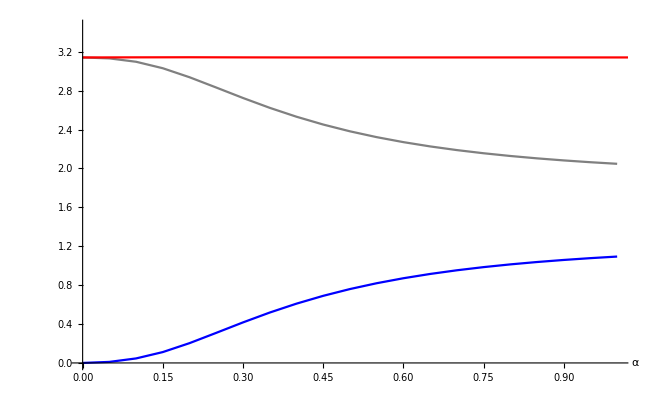

```mathematica
Show[
ListLinePlot[whiteFurnaceResult0,PlotRange->{0,1.1*π},PlotStyle->Gray,AxesLabel->{"α",""}],
ListLinePlot[whiteFurnaceResult1,PlotStyle->Blue],
ListLinePlot[whiteFurnaceResult0+whiteFurnaceResult1,PlotRange->Full,PlotStyle->Red]
]
```

### Analytical fitting (not really finished, not that much interesting anyway)

```mathematica
Clear[a,b,c,d,e,f,x,y]
fittingMethod="LevenbergMarquardt";
fittingMethod="PrincipalAxis";
fittingMethod="Automatic";

modelOrenEo=a+b*x+c*y+d*x^2+e*y^2+f*x^2*y+g*x*y^2+h*x^3+i*y^3+j*x^3*y+k*x*y^3+l*x^3*y^3;
modelOrenEo=(a+b*x+c*x^2+d*x^3) + (e+f*x+g*x^2+h*x^3)*y+ (i+j*x+k*x^2+l*x^3)*y^2+ (m+n*x+o*x^2+p*x^3)*y^3;
(*fitFuncOren[a_?NumericQ,b_?NumericQ,x_?NumericQ]:=y/.FindRoot[a y+b Log[y]==x,{y,1.}];*)
fitfunc[x_,y_,a_,b_,c_,d_,e_,f_,g_,h_,i_,j_,k_,l_,m_,n_,o_,p_]:=(a+b*x+c*x^2+d*x^3) + (e+f*x+g*x^2+h*x^3)*y+ (i+j*x+k*x^2+l*x^3)*y^2+ (m+n*x+o*x^2+p*x^3)*y^3
fitOrenEo=FindFit[resultOrenEo,fitfunc[x,y,a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p],{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p},{x,y},Method->fittingMethod]
Show[
Plot3D[fOrenEo[x,y],{x,0,1},{y,0,1},AxesLabel->{"cos(θ)", "α","E_i"}],
Plot3D[Min[1,modelOrenEo/.fitOrenEo],{x,0,1},{y,0,1},PlotStyle->Red]
]
```

{a→1.0057,b→0.0458902,c→-0.0454034,d→0.0232934,e→0.056118,f→-0.771209,g→0.21819,h→-0.286582,i→-0.93392,j→0.838325,k→-0.0236121,l→0.227303,m→0.664248,n→-0.292948,o→-0.107221,p→-0.0352586}

-Graphics3D-

```mathematica
Clear[x,y,a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q]
fitfunc[x_,y_,a_,b_,c_,d_,e_,f_,g_,h_,i_,j_,k_,l_,m_,n_,o_,p_]:=Min[1,(a+b*x+c*x^2+d*x^3) + (e+f*x+g*x^2+h*x^3)*y+ (i+j*x+k*x^2+l*x^3)*y^2+ (m+n*x+o*x^2+p*x^3)*y^3]
```

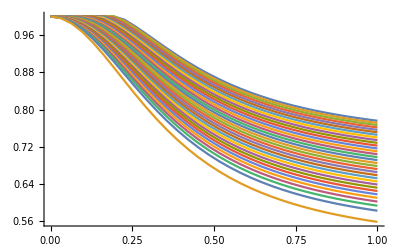

```mathematica
t=Table[{ (y-1)/(countX-1), testResultOrenEo[[1+countX*(y-1)+(x-1)]][[3]]},{x,1,countX},{y,1,countY}];
t[[1]];
ListLinePlot[t[[1]]];
Show[ListLinePlot[t]]
```

```mathematica
modelOrenEoY=a+b*y+c*y^2+d*y^3
fitsOrenEoY=Table[FindFit[t[[,modelOrenEoY,{a,b,c,d,e,f,g,h,i},{x,y},Method->fittingMethod]
Show[
Plot3D[fOrenEo[x,y],{x,0,1},{y,0,1},AxesLabel->{"cos(θ)", "α","E_i"}],
Plot3D[Min[1,modelOrenEo/.fitOrenEo],{x,0,1},{y,0,1},PlotStyle->Red]
]
```

# Fresnel Formulations

Classical dielectric Fresnel formulation from Walter / Cook&Torrance.
Note: this formulation is perfectly fine for metallic materials as long as the F_90 factor is 1, as can be seen at the bottom of this page.

```mathematica
fresnel=Function[{c,F0},
η=(1+√F0)/(1.0000001-√F0);
g=√(η^2-1+c^2);
1/2((g-c)/(g+c))^2(1+((c*(g+c)-1)/(c*(g-c)+1))^2)
];
F0=1.0;
Manipulate[Plot[fresnel[Cos[θ],F0],{θ,0,π/2},PlotRange->{0,1.1}],{{F0,1},0,1}]
```

Half-Vector formulation of Fresnel, before I understand my way of thinking is a load of bullshit... Actually, cos(θ_h) is not the cosine that is used in the Fresnel formulation of BRDFs but we must use cos(θ_d) instead!
That’s because, according to Walter, the perfect mirror condition appears when ω_h=ω_m, i.e. the half-vector is perfectly aligned with the microscopic surface’s micro-facet. Then the reflectance of the incoming light due to Fresnel only depends on the angle between the incoming light vector ω_i and the micro-facet normal ω_m=ω_h so it’s really dependent on ω_i·ω_h=cos(θ_d)...

```mathematica
fresnelH=Function[{θo,θi,F0},
lengthH=√(2+2*Cos[θo-θi]);
cosH=(Cos[θo]+Cos[θi])/lengthH;
fresnel[cosH,F0]
];
Manipulate[Plot[fresnelH[θo,θi,F0],{θi,-π/2,π/2},PlotRange->{0,1}],{{θo,0},-π/2,π/2},{{F0,1},0,1}];
Manipulate[Plot[fresnel[Cos[θo],F0]*fresnel[Cos[θi],F0],{θi,-π/2,π/2},PlotRange->{0,1}],{{θo,0},-π/2,π/2},{{F0,1},0,1}];
```

```mathematica
Manipulate[
Show[
Plot[fresnelH[θo,θi,F0],{θi,-π/2,π/2},PlotRange->{0,1}],
Plot[fresnel[Cos[θo],F0]*fresnel[Cos[θi],F0],{θi,-π/2,π/2},PlotRange->{0,1},PlotStyle->Red]
]
,{{θo,0},-π/2,π/2},{{F0,0.8},0,1}];
```

Artist-Friendly Metal Fresnel formulation, from Ole Gulbrandsen.
• Mostly similar to dielectric Fresnel except at grazing angles (use dielectric Fresnel all the way if you really always have F_90=1)
• Fails to properly account for IOR=1 and diverges from dielectric Fresnel for F_0<0.2 (you should revert to using dielectric Fresnel in these cases anyway)

```mathematica
fresnelMetal=Function[{c,F0,F90},
r=F0;
g=F90;
c2=c^2;

(* Compute n and k *)
sqrtR=√r;
nmin=(1-r)/(1+r);
nmax= (1+sqrtR)/(1-sqrtR);
n=nmin*(1-g)+nmax*g;

n2=n^2;
nr=(n+1)^2*r-(n-1)^2;
k2=nr/(1-r);

(* Compute perpendicular polarized Fresnel *)
numPe=n2+k2-2*n*c+c2;
denPe=n2+k2+2*n*c+c2;
Pe=numPe/denPe;

(* Compute parallel polarized Fresnel *)
numPa=(n2+k2)*c2-2*n*c+1;
denPa=(n2+k2)*c2+2*n*c+1;
Pa=numPa/denPa;

0.5*(Pe+Pa)
];
fresnelMetal[0.2,0.8,0.95];
```

```mathematica
fresnelSchlick=Function[{c,F0},
F0+(1-F0)*(1-c)^5
];
```

Here we show the comparison between dielectric and metallic Fresnel expressions (Schlick is given to show how it differs to more accurate versions):

```mathematica
Manipulate[
Show[
Plot[fresnelSchlick[Cos[θ],F0],{θ,0,π/2},PlotRange->{0,1.1},PlotStyle->Green]
,Plot[fresnelMetal[Cos[θ],F0,F90],{θ,0,π/2},PlotRange->{0,1}]
,Plot[fresnel[Cos[θ],F0],{θ,0,π/2},PlotRange->{0,1.1},PlotStyle->Red]
]
,{{F0,0.0 },0,0.999},{{F90,1},0,1}]
```

# Simulated Multiple-Scattering Fresnel Factor

The idea here is to use my MSBRDF simulator to cast many rays on a tiny surface and measure the total energy that comes out for several scattering orders (up to 6, the 7th order stores the total of the remaining 6+ orders).

I ran the simulation for 16 incidence angles from 0 to 90°, 16 surface roughness values and 20 F_0 values from 1 (IOR=∞) down to 0.04 (IOR= 1.5, the classical dielectric value used in many 3D engines).

Theoretically, total energy for order 1 should be roughly the energy of a Cook-Torrance BRDF (because my simulator uses a heightfield with a Beckmann distribution of heights, not a GGX distribution)(using the code from Heitz).
The sum of the energy output by all other orders should be equivalent to our magical multiple-scattering term:

	π-E_avg(α)=π-∫E_o(θ_o,α) cos(θ_o) ⅆ θ_o

The goal then is to check that it is indeed the case.
Then, we must decompose the numerical simulation of orders 2+ to understand what are their general shape (if any can be found, but an approximation will suffice) and what law governs the dependence on F_0, typically we expect order 1 to be directly linked to F_0 while order 2 should be linked to F_0^2 and subsequent order N to F_0^N.

Eventually, we’re looking for some expression that would look like this:

	E_avg^j(θ_i,α,F_0)= f(θ_i,α)·g(j)·(h(F_0))^j

f(θ_i,α) is some general expression we don’t really care about since the ∑_(j=2)^∞ E_avg^j(θ_i,α,F_0=1)=π-E_avg(α)
g(j) is some amplitude function depending on the order j
h(F_0) is some mapping from F_0 to an expression that can be raised to the power of the current order

```mathematica
SetDirectory["D:\\Workspaces\\GodComplex\\Tests\\TestMSBRDF\\Tables"]; 
countTheta = 16;
countRoughness= 16;
countF0=20;
countOrders=7;
taRawTotalReflectances=Table[
Import["TotalReflectance_"  <>ToString[countTheta] <>"x"  <>ToString[countRoughness] <>"x"  <>ToString[countF0] <>"_order"  <>ToString[order] <>".bin", "Real64"],{order,1,countOrders}];
```

```mathematica
Table[{N[Mod[i-1,countTheta]/countTheta*π/2],N[1-Quotient[i-1,countTheta]/(countRoughness-1)],taRawTotalReflectances[[1]][[i]]},{i,1,countTheta*countRoughness}];
Length[taRawTotalReflectances[[1]]]
```

5120

```mathematica
taTotalReflectances=Table[
Table[
Table[{N[Mod[i-1,countTheta]/countTheta*π/2],N[1-Quotient[i-1,countTheta]/(countRoughness-1)],taRawTotalReflectances[[order]][[k*countTheta*countRoughness+ i]]},{i,1,countTheta*countRoughness}]
,{k,0,countF0-1}]
,{order,1,countOrders}];
```

```mathematica
Manipulate[
ListPlot3D[taTotalReflectances[[order]][[F0]],PlotRange->{0,order^2*10^(-order+1)},AxesLabel->{"θ","α"}],{{order,2},1,countOrders,1},{F0,1,countF0,1}
]
```

Part::partd: Part specification taTotalReflectances ⟦ 2 ⟧ is longer than depth of object.

ListPlot3D::arrayerr: taTotalReflectances must be a valid array or a list of valid arrays.

## Show Total Reflectance Depending on F_0

```mathematica
taSum=Table[
Table[{N[Mod[i-1,countTheta]/countTheta*π/2],N[1-Quotient[i-1,countTheta]/(countRoughness-1)],
Sum[taRawTotalReflectances[[order]][[k*countTheta*countRoughness+ i]],{order,1,countOrders}]
},{i,1,countTheta*countRoughness}]
,{k,0,countF0-1}];
Manipulate[ListPlot3D[taSum[[F0]],PlotRange->{0,1},AxesLabel->{"θ","α"}],{F0,1,countF0,1}]
```

Part::partd: Part specification taSum ⟦ 1 ⟧ is longer than depth of object.

ListPlot3D::arrayerr: taSum ⟦ 1 ⟧ must be a valid array or a list of valid arrays.

```mathematica
taSum2=Table[
Table[{N[Mod[i-1,countTheta]/countTheta*π/2],N[1-Quotient[i-1,countTheta]/(countRoughness-1)],
Sum[taRawTotalReflectances[[order]][[k*countTheta*countRoughness+ i]],{order,2,countOrders}]
},{i,1,countTheta*countRoughness}]
,{k,0,countF0-1}];
Manipulate[ListPlot3D[taSum2[[F0]],PlotRange->{0,0.5},AxesLabel->{"θ","α"}],{F0,1,countF0,1}]
```

Part::partd: Part specification taSum2 ⟦ 1 ⟧ is longer than depth of object.

ListPlot3D::arrayerr: taSum2 ⟦ 1 ⟧ must be a valid array or a list of valid arrays.

## Verifying sum of

# Simulated Multiple-Scattering Diffuse Reflectance Factor

```mathematica
SetDirectory["D:\\Workspaces\\GodComplex\\Tests\\TestMSBRDF\\Tables"]; 
countTheta = 16;
countRoughness= 16;
countAlbedo=20;
countOrders=7;
taRawTotalDiffuseReflectances=Table[
Import["TotalReflectance_Diffuse_Cosine_"  <>ToString[countTheta] <>"x"  <>ToString[countRoughness] <>"x"  <>ToString[countAlbedo] <>"_order"  <>ToString[order] <>".bin", "Real64"],{order,1,countOrders}];
```

Generate list interpolations

```mathematica
fTotalReflectance=Table[
ListInterpolation[Table[
taRawTotalDiffuseReflectances[[order]][[countTheta*((roughness-1)+countRoughness*(albedo-1))+theta]],{theta,1,countTheta},{roughness,1,countRoughness},{albedo,1,countAlbedo}],{{0,π/2},{1,0},{1,0}}],
{order,1,countOrders}];
```

```mathematica
Manipulate[
Plot3D[fTotalReflectance[[order]][x,α,albedo],{x,0,π/2},{α,0,1},PlotRange->{0,3.5^(-order+1)}],{{albedo,1},0,1},{order,1,countOrders,1}]
```

```mathematica
(*taTotalDiffuseReflectances=Table[
Table[
Table[{N[Mod[i-1,countTheta]/countTheta*π/2],N[1-Quotient[i-1,countTheta]/(countRoughness-1)],taRawTotalDiffuseReflectances[[order]][[k*countTheta*countRoughness+ i]]},{i,1,countTheta*countRoughness}]
,{k,0,countAlbedo-1}]
,{order,1,countOrders}];
Manipulate[
ListPlot3D[taTotalDiffuseReflectances[[order]][[Albedo]],PlotRange->{0,3.5^(-order+1)},AxesLabel->{"θ","α"}],{{order,2},1,countOrders,1},{Albedo,1,countAlbedo,1}
]*)
```

## Show Total Reflectance Depending on Albedo

```mathematica
(*taSumDiffuse=Table[
Table[{N[Mod[i-1,countTheta]/countTheta*π/2],N[1-Quotient[i-1,countTheta]/(countRoughness-1)],
Sum[taRawTotalDiffuseReflectances[[order]][[k*countTheta*countRoughness+ i]],{order,1,countOrders}]
},{i,1,countTheta*countRoughness}]
,{k,0,countAlbedo-1}];
Manipulate[ListPlot3D[taSumDiffuse[[Albedo]],PlotRange->{0,1},AxesLabel->{"θ","α"}],{Albedo,1,countAlbedo,1}]*)
```

```mathematica
Manipulate[Plot3D[Sum[fTotalReflectance[[order]][x,α,albedo],{order,1,countOrders}],{x,0,π/2},{α,0,1},PlotRange->{0,1},AxesLabel->{"θ","α"}],{{albedo,1},0,1}]
```

```mathematica
(*taSumDiffuse2=Table[
Table[{N[Mod[i-1,countTheta]/countTheta*π/2],N[1-Quotient[i-1,countTheta]/(countRoughness-1)],
Sum[taRawTotalDiffuseReflectances[[order]][[k*countTheta*countRoughness+ i]],{order,2,countOrders}]
},{i,1,countTheta*countRoughness}]
,{k,0,countAlbedo-1}];
Manipulate[ListPlot3D[taSumDiffuse2[[Albedo]],PlotRange->{0,0.3},AxesLabel->{"θ","α"}],{Albedo,1,countAlbedo,1}]*)
```

```mathematica
Manipulate[Plot3D[Sum[fTotalReflectance[[order]][x,α,albedo],{order,2,countOrders}],{x,0,π/2},{α,0,1},PlotRange->{0,0.3},AxesLabel->{"θ","α"}],{{albedo,1},0,1}]
```

Visualizing each individual order

```mathematica
Manipulate[
Show[
Table[
Plot3D[fTotalReflectance[[order]][x,α,albedo],{x,0,π/2},{α,0,1},
PlotRange->{0,0.15},PlotStyle->Hue[(4*(order-2))/countOrders]],{order,2,countOrders}]
],
{{albedo,1},0,1}]
```

## White Furnace Comparison

We computed the total energy bouncing off the surface at various scattering orders for different values of roughness, incidence angle and albedos.
So basically we performed:

	E(ω_i,α,ρ)=∫_(Ω^+) L_i(ω_i) f_r( ω_o,ω_i,α,ρ)(ω_o·n)dω_o
	
With L_i(ω_i)=1
To compute the equivalent white furnace test we thus need to compute:

	E_total(α,ρ)=∫_(Ω^+) E(ω_i,α,ρ)(ω_i·n)dω_i

```mathematica
whiteFurnaceSimul[α_,ρ_]:=2*π*NIntegrate[Sum[fTotalReflectance[[order]][θi,α,ρ],{order,2,countOrders}]*Cos[θi]*Sin[θi],{θi,0,π/2},WorkingPrecision->MachinePrecision];
```

```mathematica
Plot[fTotalReflectance[[2]][θi,1,1],{θi,0,π/2},PlotRange->{0,0.2}];
whiteFurnaceSimul[1,1]
```

0.701024

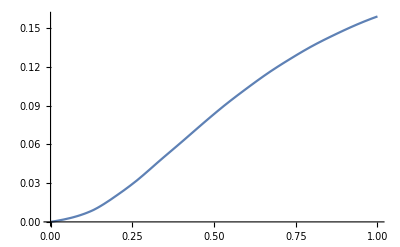

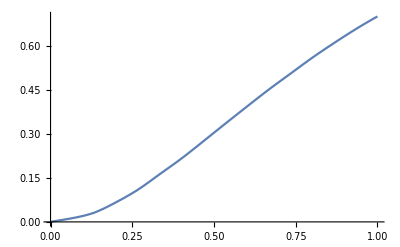

```mathematica
θ=0;
albedo=1;
Plot[fTotalReflectance[[2]][θ,α,albedo],{α,0,1}]
Plot[whiteFurnaceSimul[α,albedo],{α,0,1}]
```

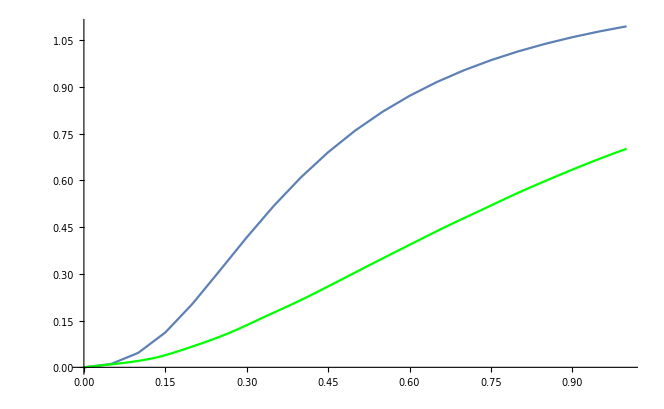

```mathematica
Show[
ListLinePlot[whiteFurnaceResult1]
(*,Plot[Sum[fTotalReflectance[[order]][θ,α,albedo],{order,2,countOrders}],{α,0,π},PlotStyle->Red]*)
,Plot[whiteFurnaceSimul[α,albedo],{α,0,1},PlotStyle->Green]
]
```

We see here the green curve is not exactly identical to the white furnace result given by the theoretical multiple-scattering expression for the Oren-Nayar BRDF. Maybe it’s due to the many simplifications of the Oren-Nayar model? Maybe there’s a bias in my simulation?
Overall, we won’t linger too much on these differences and assume the simulation represents ground-truth data.

## Finding an Analytical Model

We saw that integrating our order 2^+ irradiance values (the green curve in the above graph) yields π-E_total where E_total(α,ρ) is the total irradiance reflected for the single-scattering Oren-Nayar BRDF.

We are interested in how each order contributes to that complement.
We assume the roughness-dependent shape is not important and concentrate on the maximum values of the white furnace functions for each order, when α=1. But we are interested in the evolution of that maximum value when varying the albedo.

So let’s create a table of samples of white furnace values for varying albedos, for each order (except last order, which is a compound of all remaining orders and doesn’t interest us):

```mathematica
α=1;
taWhiteFurnaceDiffuse=
Table[2*π*NIntegrate[fTotalReflectance[[order]][θi,α,ρ]*Cos[θi]*Sin[θi],{θi,0,π/2},WorkingPrecision->MachinePrecision],{order,2,countOrders-1},{ρ,0,1,0.02}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate :: izero will be suppressed during this calculation.

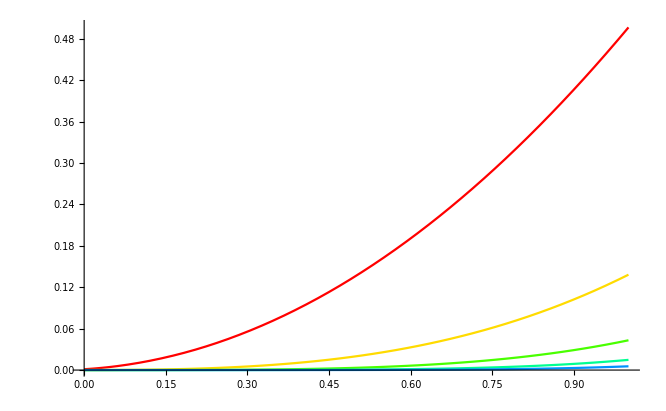

```mathematica
fWhiteFurnaceDiffuse=Table[ListInterpolation[taWhiteFurnaceDiffuse[[order-1]],{0,1}],{order,2,countOrders-1}];
Show[Table[Plot[fWhiteFurnaceDiffuse[[order-1]][ρ],{ρ,0,1},PlotRange->Full,PlotStyle->Hue[(order-2)/countOrders]],{order,2,countOrders-1}]]
```

Now let’s try and fit each curve with a polynomial of the form f(ρ)=a_n*ρ^n where n is the order:

```mathematica
Clear[a,b,c,d,x]
fittingMethod="LevenbergMarquardt";
fittingMethod="PrincipalAxis";
fittingMethod="Automatic";

fitter=Function[{order},
model=a*x^order;
data=Table[{ρ,fWhiteFurnaceDiffuse[[order-1]][ρ]},{ρ,0,1,0.01}];
fit=FindFit[data,model,{a,b,c,d,e},x,Method->fittingMethod];
Function[x,Evaluate[model/.fit]];
a/.fit
];

fitter[3]
```

0.141632

```mathematica
values=Table[fitter[order],{order,2,countOrders-1}]
```

{0.508918,0.141632,0.0442183,0.0151468,0.00559481}

```mathematica
Manipulate[
Show[
Plot[fWhiteFurnaceDiffuse[[order-1]][ρ],{ρ,0,1},PlotRange->{0,fWhiteFurnaceDiffuse[[order-1]][1]},AxesLabel->{"ρ","E_avg"}]
,Plot[values[[order-1]]*ρ^order,{ρ,0,1},PlotStyle->Red]
],{order,2,countOrders-1,1}]
```

## Gna

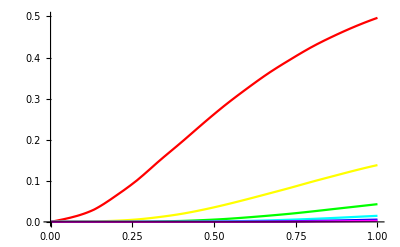

```mathematica
ρ=1;
Show[
Table[Plot[2*π*NIntegrate[fTotalReflectance[[order]][θi,α,ρ]*Cos[θi]*Sin[θi],{θi,0,π/2},WorkingPrecision->MachinePrecision],{α,0,1},PlotRange->{0,0.5},PlotStyle->Hue[(order-2)/(countOrders-1)]],
{order,2,countOrders}]
]
```